```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
rho=Flatten[Import["./kappa.dat"]];
k=Flatten[Import["./k1.dat"]];
rhobar=rho/k;
```

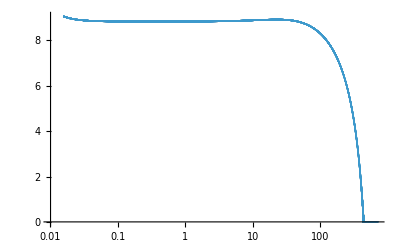

```mathematica
ListPlot[Transpose[{k,rhobar}],PlotRange->All,ScalingFunctions->{"Log",Automatic}]
```